```mathematica
solution =DSolve[f'[t]==96/5 * Pi^(8/3)*Mc^(5/3)*f[t]^(11/3),f[t],t]
```

{{f[t]→15^(3/8)/(2 2^(1/8) (-96 Mc^(5/3) π^(8/3) t-5 C[1])^(3/8))}}

```mathematica
f[t_]=f[t]/. solution[[1]]
```

15^(3/8)/(2 2^(1/8) (-96 Mc^(5/3) π^(8/3) t-5 C[1])^(3/8))

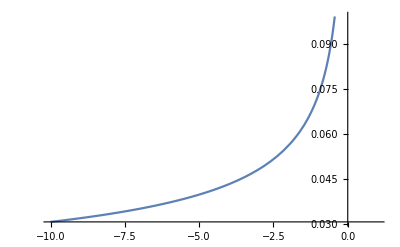

```mathematica
Plot[f[t]/.{C[1]->0, Mc->1},{t,-10,1}]
```

```mathematica
solutionorb =DSolve[w'[t]==96/5 *Mc^(5/3)*w[t]^(11/3),w[t],t]
```

{{w[t]→15^(3/8)/(2 2^(1/8) (-96 Mc^(5/3) t-5 C[1])^(3/8))}}

```mathematica
solutionorb1PN =DSolve[w'[t]==96/5 *Mc^(5/3)*w[t]^(11/3)(1 - (743/336 + 11*mu/(4*M))*M*w[t]^(2/3)),w[t],t]
```

{{w[t]→InverseFunction[1/8564980580352(3 (743 M+924 mu)^4 Log[336-(743 M+924 mu) #1^(2/3)]-2 (743 M+924 mu)^4 Log[#1]+9559130112/#1^(8/3)+(37933056 (743 M+924 mu))/#1^2+(169344 (743 M+924 mu)^2)/#1^(4/3)+(1008 (743 M+924 mu)^3)/#1^(2/3))&][-2/35 Mc^(5/3) t+C[1]]}}

```mathematica
solutionorb1PNnumerical = NDSolve[{w'[t]==96/5 *Mc^(5/3)*w[t]^(11/3)(1 - (743/336 + 11*mu/(4*M))*M*w[t]^(2/3)), w[10]==1},w,{t, -4000, -1}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 10..

NDSolve[{w'[t]==96/5 Mc^(5/3) (1-M (743/336+(11 mu)/(4 M)) w[t]^(2/3)) w[t]^(11/3),w[10]==1},w,{t,-4000,-1}]